## Verify the problem associated with Zemax Physical Optics Propagation

Different Options in order to debug:
data: Huygens PSF of ideal lens
data2: Fourier transform of a circular aperture
data3: POP top hat going through ideal lens
data4: ω = 16 mm Gaussian beam going through ideal lens (D=45mm)
data5: ω = 16 mm Gaussian beam going through AL50100H
data6: Huygens PSF of AL50100H.

Everything makes sense, except data5. The combination of POP and AL50100H gives wrong prediction. Even Huygens PSF gives correct result. Assume that somewhere along the propagation the beam is under-sampled?

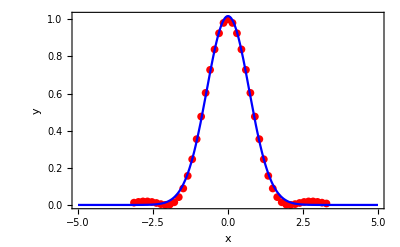

{a→1.01754,μ→1.31331×10^-7,σ→1.4173}

```mathematica
(*This is Huygens FFT of Paraxial lens 45 mm aperture*)
data={{-3.13288,0.012328},{-2.9837,0.016421},{-2.83451,0.018952},{-2.68533,0.018955},{-2.53614,0.016016},{-2.38696,0.010624},{-2.23777,0.004421},{-2.08859,0.000277},{-1.9394,0.002123},{-1.79022,0.014546},{-1.64103,0.042148},{-1.49185,0.088783},{-1.34266,0.156761},{-1.19348,0.246169},{-1.04429,0.354437},{-0.89511,0.476257},{-0.74592,0.603903},{-0.59674,0.727941},{-0.44755,0.838242},{-0.29837,0.925185},{-0.14918,0.980842},{0,1},{0.14918,0.980842},{0.29837,0.925185},{0.44755,0.838242},{0.59674,0.727941},{0.74592,0.603903},{0.89511,0.476257},{1.04429,0.354437},{1.19348,0.246169},{1.34266,0.156761},{1.49185,0.088783},{1.64103,0.042148},{1.79022,0.014546},{1.9394,0.002123},{2.08859,0.000277},{2.23777,0.004421},{2.38696,0.010624},{2.53614,0.016016},{2.68533,0.018955},{2.83451,0.018952},{2.9837,0.016421},{3.13288,0.012328},{3.28207,0.007818}};

(*高斯函数拟合*)
fit=NonlinearModelFit[data,a Exp[-2*(x-μ)^2/(σ^2)],{a,μ,σ},x];

(*显示拟合结果*)
Show[ListPlot[data,PlotStyle->Red,PlotMarkers->{Automatic,8}],Plot[fit[x],{x,-5,5},PlotStyle->Blue],PlotRange->All,Frame->True,FrameLabel->{"x","y"}]
fit["BestFitParameters"]
```

```mathematica
(*This is the Fourier Transform of a circle aperture, which should be [Subscript[J, 1](kr)/kr]^2, yes it is. But somehow Zemax FFT is not Bessel function. Slightly different*)
List2={2.52897×10^6,2.5060463704649066*^6,2.4383069332333873*^6,2.328795589692614*^6,2.1823698748634495*^6,2.0053996462989927*^6,1.8053755558972522*^6,1.590457778623505*^6,1.368998028766416*^6,1.149069020870392*^6,938033.9504293742,742184.4547214289,566469.1526817186,414327.03272265714,287631.2209271263,186739.910537141,110643.15143691516,57187.46513268899,23355.392965656367,5574.423924119663,29.36788157783622,2954.088017979789,10882.239978063544,20841.856139309606,30484.701715454386,38147.686888377044};
List2=List2/List2[[1]]
Data2=Table[{(i-1)*0.1,List2[[i]]},{i,1,Length[List2]}];
```

{1.,0.990936,0.96415,0.920847,0.862948,0.792971,0.713878,0.628895,0.541326,0.454362,0.370915,0.293473,0.223992,0.163832,0.113735,0.0738403,0.0437503,0.0226129,0.00923514,0.00220423,0.0000116126,0.0011681,0.00430303,0.00824124,0.0120542,0.0150843}

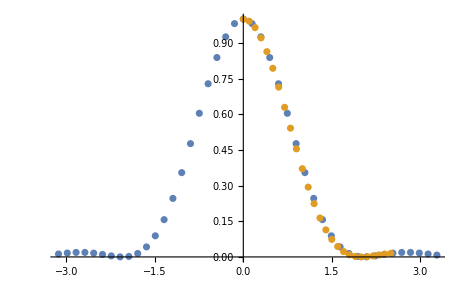

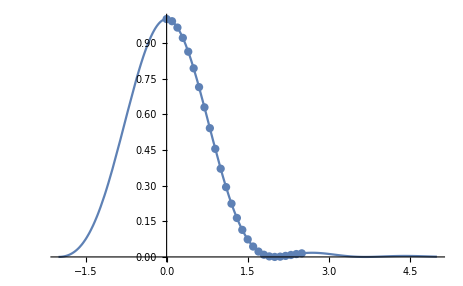

```mathematica
ListPlot[{data,Data2}]
fac=(0.45*Pi/0.741);
Show[Plot[4*(BesselJ[1,fac*r]/(fac*r))^2,{r,-2,5}],ListPlot[Data2]]
```

```mathematica
fit2=NonlinearModelFit[Data2,a* Exp[-2*(x)^2/(σ^2)],{a,σ},x];
fit2["BestFitParameters"]
```

{a→1.0155,σ→1.38693}

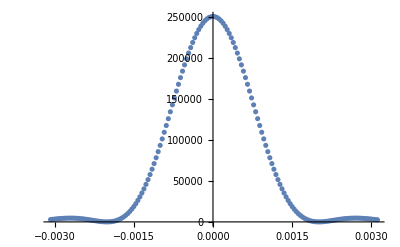

{a→1.02092,σ→1.38908,μ→8.25201×10^-8}

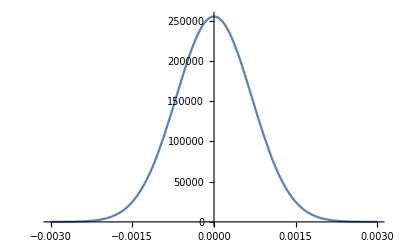

```mathematica
(*This is Top hat 45 mm going through paraxial lens, agrees with the airy disk fit very well*)

data3=Import["D:\\MIT2023\\provezemax.xlsx"];
data3=Flatten[data3,1];
ListPlot[data3]
fit3=NonlinearModelFit[data3,a* 250000*Exp[-2*(1000*x-μ)^2/(σ^2)],{a,σ,μ},x];
fit3["BestFitParameters"]
Plot[fit3[x],{x,-0.003,0.003}]
```

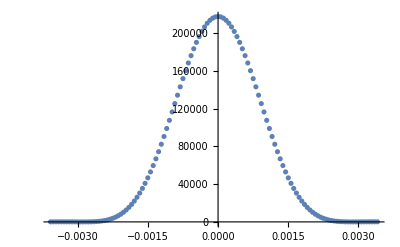

{a→0.879044,σ→1.71144,μ→-1.70565×10^-8}

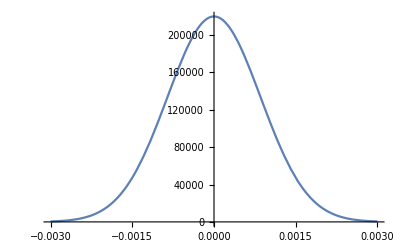

```mathematica
(*Use 16 mm Gaussian beam and 45 mm aperture, gives us 1.72 um waist. Perfect as predicted by Fourier Transform*)
data4=Import["D:\\MIT2023\\provezemax2.xlsx"];
data4=Flatten[data4,1];
ListPlot[data4]
fit4=NonlinearModelFit[data4,a* 250000*Exp[-2*(1000*x-μ)^2/(σ^2)],{a,σ,μ},x];
fit4["BestFitParameters"]
Plot[fit4[x],{x,-0.003,0.003}]
```

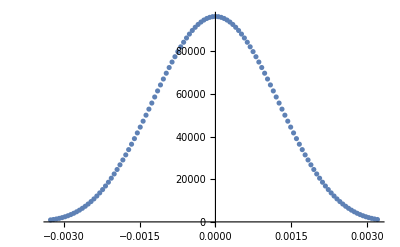

{a→0.389065,σ→2.34244,μ→0.0000425869}

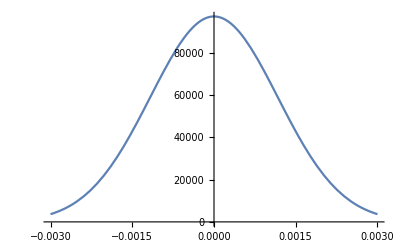

```mathematica
(*This is AL50100H 16 mm Gaussian Beam at focus. Quite large, but why*)
data5=Import["D:\\MIT2023\\provezemax2.xlsx"];
data5=Flatten[data5,1];
ListPlot[data5]
fit5=NonlinearModelFit[data5,a* 250000*Exp[-2*(1000*x-μ)^2/(σ^2)],{a,σ,μ},x];
fit5["BestFitParameters"]
Plot[fit5[x],{x,-0.003,0.003}]
```

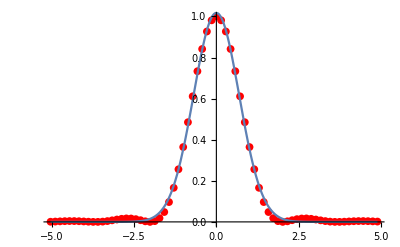

{a→1.01754,μ→1.31331×10^-7,σ→1.4173}

```mathematica
(*This is Huygens FFT of AL50100H, in fact is the same as Paraxial lens*)

data6={{-5.04474,0.000763},{-4.90061,0.001647},{-4.75647,0.002661},{-4.61234,0.003551},{-4.4682,0.004059},{-4.32407,0.003999},{-4.17993,0.003333},{-4.0358,0.002215},{-3.89166,0.00099},{-3.74752,0.000134},{-3.60339,0.000138},{-3.45925,0.001369},{-3.31512,0.003926},{-3.17098,0.007538},{-3.02685,0.011553},{-2.88271,0.015025},{-2.73858,0.016927},{-2.59444,0.016446},{-2.4503,0.013332},{-2.30617,0.008215},{-2.16203,0.002826},{-2.0179,0.000044},{-1.87376,0.003715},{-1.72963,0.018247},{-1.58549,0.047997},{-1.44136,0.096538},{-1.29722,0.165913},{-1.15308,0.256001},{-1.00895,0.364129},{-0.86481,0.48501},{-0.72068,0.611067},{-0.57654,0.733123},{-0.43241,0.841379},{-0.28827,0.926551},{-0.14414,0.98101},{0,0.999745},{0.14414,0.98101},{0.28827,0.926551},{0.43241,0.841379},{0.57654,0.733123},{0.72068,0.611067},{0.86481,0.48501},{1.00895,0.364129},{1.15308,0.256001},{1.29722,0.165913},{1.44136,0.096538},{1.58549,0.047997},{1.72963,0.018247},{1.87376,0.003715},{2.0179,0.000044},{2.16203,0.002826},{2.30617,0.008215},{2.4503,0.013332},{2.59444,0.016446},{2.73858,0.016927},{2.88271,0.015025},{3.02685,0.011553},{3.17098,0.007538},{3.31512,0.003926},{3.45925,0.001369},{3.60339,0.000138},{3.74752,0.000134},{3.89166,0.00099},{4.0358,0.002215},{4.17993,0.003333},{4.32407,0.003999},{4.4682,0.004059},{4.61234,0.003551},{4.75647,0.002661},{4.90061,0.001647}};

model6=a Exp[-((x-μ)^2/(2 σ^2))];
fit6=NonlinearModelFit[data6,model6,{a,μ,σ},x];

Show[ListPlot[data6,PlotStyle->Red,PlotMarkers->{Automatic,8}],Plot[fit6[x],{x,Min[data6[[All,1]]],Max[data6[[All,1]]]}]]
fit["BestFitParameters"]
```